### Scratch

```mathematica
Module[
{many=100,deep=250,cut=200,ru,life,one,evo,data},
SeedRandom[426778];
one=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
Show[
ListLinePlot[
ParallelTable[
SeedRandom[2524+i];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
Last/@evo
,{i,many}],
PlotRange->All,AspectRatio->1/4,Frame->True
],
ListPlot[Last/@one,PlotStyle->Black]
]
]
```

```mathematica
Module[
{many=100,deep=1000,cut=200,ru,life,one,evo,data},
SeedRandom[426778];
one=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
Show[
ListLinePlot[
ParallelTable[
SeedRandom[2524+i];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
Last/@evo
,{i,many}],
PlotRange->All,AspectRatio->1/4,Frame->True
],
ListPlot[Last/@one,PlotStyle->Black]
]
]
```

```mathematica
Module[
{goal=50,deep=5000,cut=200,ru,life,evo,res},
SeedRandom[23563];
res=ParallelTable[
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#],1],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life!=-Infinity&&Abs[life-goal
]<=Abs[Last[#]-goal],{ru,life},#]
]&,{{0,3,1},0},deep];evo,100];
ListStepPlot[(Last/@#)&/@res,
Frame->True,AspectRatio->1/3]
]
```

```mathematica
Module[
{many=100,deep=1000,cut=200,ru,life,one,evo,data},
SeedRandom[426778];
one=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
Show[
ListLinePlot[
ParallelTable[
SeedRandom[2524+i];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
Last/@evo
,{i,many}],
PlotRange->All,AspectRatio->1/4,Frame->True
],
ListPlot[Last/@one,PlotStyle->Black]
]
]
```

### Actual run

```mathematica
$CloudUserID
```

willemnielsen1@gmail.com

```mathematica
runs = Module[
{many=100,deep=1000,cut=200,ru,life,one,evo,data},
ParallelTable[
SeedRandom[2524+i];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep]
,{i,many}]];
```

```mathematica
Iconize[runs]
```

```mathematica
runs = ;
```

```mathematica
runs[[1, -1, 1]]
```

{1796306308839,3,1}

```mathematica
Length[runs[[All, -1, 1]]]
```

100

```mathematica
RandomSample[runs[[All, -1, 1]], 10]
```

{{4112813941404,3,1},{1566896620542,3,1},{5031404456247,3,1},{4264709504280,3,1},{3984241889214,3,1},{4098474337227,3,1},{3288193326243,3,1},{2095833015654,3,1},{1796306308839,3,1},{7431740841114,3,1}}

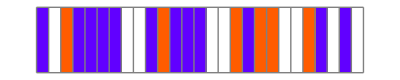
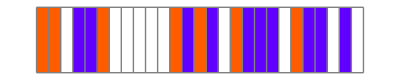
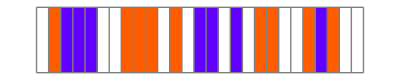
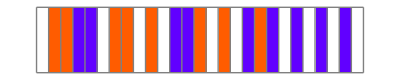
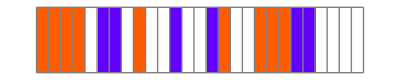
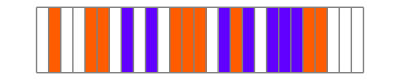
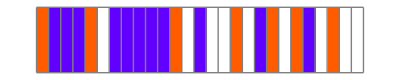
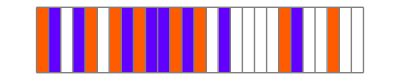

```mathematica
plotrule/@ RandomSample[runs[[All, -1, 1]], 100]
```

#### Rule Frequency Chart

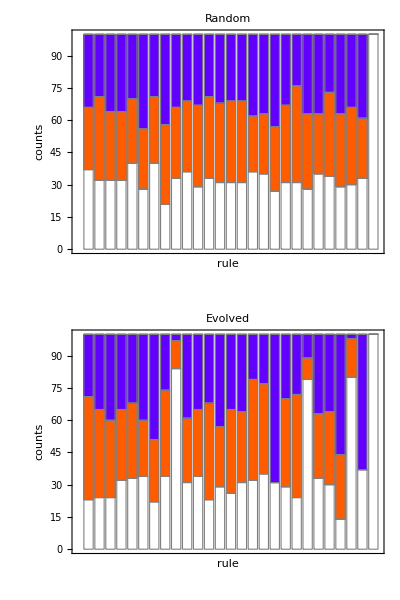

```mathematica
Column[MapThread[Function[{digs,label},With[{aps=Rasterize[ArrayPlot[List/@#,ImageSize->{10,25},ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"](*,Mesh->True,MeshStyle->Opacity[.4]*)]]&/@RuleTuples[3,1]},BarChart[BinCounts[#,{0,4,1}]&/@Transpose[digs],ChartLayout->"Stacked",ChartBaseStyle->EdgeForm[Thickness[.1]],ChartStyle->(Directive[EdgeForm[Directive[Opacity[1],Gray]],#]&)/@{{"[◼]", "CustomStyleData"}}["Colors"][[All,2]],ChartLabels->{aps,None},LabelingSize->35,AspectRatio->.4,ImageSize->{600,Automatic},Frame->True,FrameLabel->{"rule","counts"},PlotLabel->label]]],{{(Append[#,0]&/@RandomChoice[{0,1,2},{100,3^(2*1+1)-1}]),Module[{digits,n,k,r},{n,k,r}=interpretrule[#];
digits=IntegerDigits[n,k,k^(2r+1)]]&/@runs[[All, -1, 1]]},{"Random","Evolved"}}]]
```

#### Rule plot distribution

```mathematica
FeatureSpacePlot[plotrule/@ runs[[All, -1, 1]]]
```

-Graphics-

#### Pattern distribution

```mathematica
FeatureSpacePlot[Module[{ca = ArrayPad[#, 1]&/@CellularAutomaton[#, {{1}, 0}, 175], lt},
lt  = {{"[◼]", "TestCALifeTime"}}[ca];
 ArrayPlot[ca[[;;lt + 1]], ColorRules-> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}, ImageSize->{Automatic,25 Sqrt[1+lt]}]]&/@ runs[[All, -1, 1]]]
```

-Graphics-

#### Lifetime changes

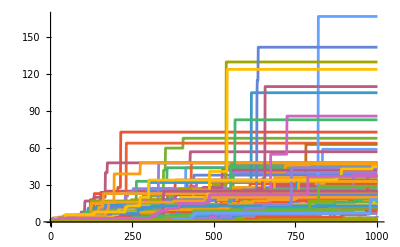

```mathematica
ListLinePlot[ runs[[All, All, -1]], PlotRange->All]
```

### Running for width:

```mathematica
widthruns = Module[
{many=100,deep=1000,cut=200,ru,life,one,evo,data, lw},
ParallelTable[
SeedRandom[2524+i];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#],1,"Symmetric"->True],
lw={{"[◼]", "CALifetimeWidth"}}[ru,cut],
If[lw[[1]]!=-Infinity&&lw[[2]]>=Last[#][[2]],{ru,lw},#]
]&,{{0,3,1},{1,1}},deep]
,{i,many}]];
```

```mathematica
Iconize[widthruns]
```

#### Rule Frequency Chart

```mathematica
Column[MapThread[Function[{digs,label},With[{aps=Rasterize[ArrayPlot[List/@#,ImageSize->{10,25},ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"](*,Mesh->True,MeshStyle->Opacity[.4]*)]]&/@RuleTuples[3,1]},BarChart[BinCounts[#,{0,4,1}]&/@Transpose[digs],ChartLayout->"Stacked",ChartBaseStyle->EdgeForm[Thickness[.1]],ChartStyle->(Directive[EdgeForm[Directive[Opacity[1],Gray]],#]&)/@{{"[◼]", "CustomStyleData"}}["Colors"][[All,2]],ChartLabels->{aps,None},LabelingSize->35,AspectRatio->.4,ImageSize->{600,Automatic},Frame->True,FrameLabel->{"rule","counts"},PlotLabel->label]]],{{(Append[#,0]&/@RandomChoice[{0,1,2},{100,3^(2*1+1)-1}]),Module[{digits,n,k,r},{n,k,r}=interpretrule[#];
digits=IntegerDigits[n,k,k^(2r+1)]]&/@widthruns[[All, -1, 1]]},{"Random","Evolved"}}]]
```

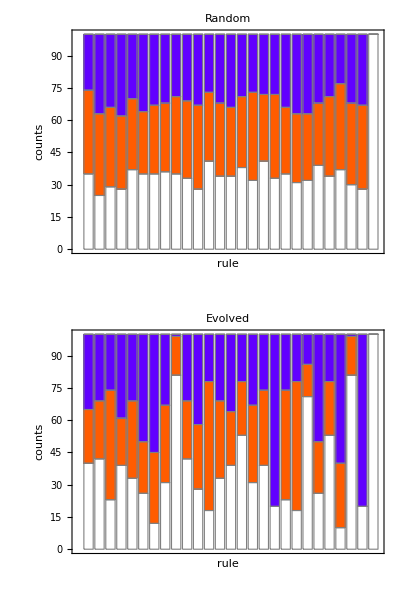

#### Pattern distribution

```mathematica
FeatureSpacePlot[Module[{ca = ArrayPad[#, 1]&/@CellularAutomaton[#, {{1}, 0}, 200], lt},
lt  = {{"[◼]", "TestCALifeTime"}}[ca];
 ArrayPlot[ca[[;;lt + 1]], ColorRules-> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}, ImageSize->{Automatic,25 Sqrt[1+lt]}]]&/@ widthruns[[All, -1, 1]]]
```

-Graphics-

### Trying to predict whether a rule is random (no immunity), adapted (width immunity), or adapted (height immunity)

```mathematica
SeedRandom[444555];
rand = Append[#,0]&/@RandomChoice[{0,1,2},{100,3^(2*1+1)-1}];
widthdigs = Module[{digits,n,k,r},{n,k,r}=interpretrule[#];
digits=IntegerDigits[n,k,k^(2r+1)]]&/@widthruns[[All, -1, 1]];
heightdigs = Module[{digits,n,k,r},{n,k,r}=interpretrule[#];
digits=IntegerDigits[n,k,k^(2r+1)]]&/@runs[[All, -1, 1]];
all = Join[Thread[rand->"Random"], Thread[widthdigs->"Width"], Thread[heightdigs->"Height"]];
```

```mathematica
SeedRandom[5555];
trainidxs = RandomSample[Range[Length[all]], 250];
testidxs = RandomSample[Delete[Range[Length[all]], List/@ trainidxs], All];
```

```mathematica
cf = Classify[all[[trainidxs]]]
```

ClassifierFunction[…]

```mathematica
cs  = cf/@ all[[testidxs, 1]];
```

```mathematica
With[{bools = MapThread[If[#1 === #2, True, False]&, {cs, all[[testidxs, 2]]}]},
N[Count[bools, True]/ Length[bools]]]
```

0.8

```mathematica
With[{bools = MapThread[If[#1 == #2, True, False]&, {RandomChoice[{"Random", "Width", "Height"}, 50], all[[testidxs, 2]]}]},
N[Count[bools, True]/ Length[bools]]]
```

0.28

```mathematica
PieChart[Counts[all[[testidxs, 2]]], ChartLabels->Automatic]
```

-Graphics-

### Feature Space Plot of all

```mathematica
With[{ca = CellularAutomaton[#, {{1}, 0}, 200]},ArrayPlot[ca[[;;All]]]]&/@({FromDigits[#,3],3,1}&/@ rand)
```

```mathematica
Module[{ca = ArrayPad[#, 1]&/@CellularAutomaton[#, {{1}, 0}, 200], lt},
lt  = {{"[◼]", "TestCALifeTime"}}[ca];
ArrayPlot[ca[[;;If[lt == -Infinity, All, lt + 1]]], ColorRules-> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}, ImageSize->{Automatic,25 Sqrt[1+If[lt == -Infinity, 15, lt]]}]]&/@Join[widthruns[[All, -1, 1]], runs[[All, -1, 1]], {FromDigits[#,3],3,1}&/@ rand]
```

```mathematica
FeatureSpacePlot[
Module[{ca = ArrayPad[#, 1]&/@CellularAutomaton[#, {{1}, 0}, 200], lt},
lt  = {{"[◼]", "TestCALifeTime"}}[ca];
ArrayPlot[ca[[;;If[lt == -Infinity, All, lt + 1]]], ColorRules-> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}, ImageSize->{Automatic,25 Sqrt[1+If[lt == -Infinity, 15, lt]]}]]&/@Join[widthruns[[All, -1, 1]], runs[[All, -1, 1]], {FromDigits[#,3],3,1}&/@ rand]
]
```

-Graphics-

```mathematica
rand = Append[#,0]&/@RandomChoice[{0,1,2},{100,3^(2*1+1)-1}];
```

```mathematica
SeedRandom[5555];
GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[{FromDigits[#,4],4,1},{{1},0},{200,{-200,200}}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@(Append[#,0]&/@RandomChoice[{0,1,2,3},{15,4^(2*1+1)-1}]),3],ImageSize->{600,Automatic}]
```